```mathematica
<<MaTeX`
```

## Первое приближение

```mathematica
ClearAll[GetP];
GetP[T_] := 133.32 10^(10.3454 -8345.57/T-8.84 10^-5 T - 0.68106 Log10[T]);
```

```mathematica
ν0 = (3. 10^8)/(670 10^-9)/10^6; (* МГц *)
c = 3 10^8; (* м/c *)
Γ = 6 10^6 /10^6(* МГц *);
vQ = 1200;(* м/c *)
kB = 1.38 10^-23;
T = 300 + 273;
l = 0.1;
n =GetP[T]/(kB T);
```

```mathematica
Na = 6.02 10^23;
R = Na kB;
m = 0.007 / Na;
M = 0.007;
```

```mathematica
Γ/ν0 c
```

4.02

## Первый вариант

```mathematica
ClearAll[ν0, c, Γ, vQ];
```

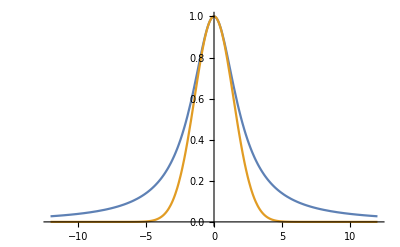

```mathematica
Plot[{ 1/(1 + 4 (ν0 - ν0(1- v/c))^2/Γ^2), Exp[- (4 (ν0 - ν0(1- v/c))^2)/Γ^2]}, {v, -0.01vQ, 0.01 vQ}, PlotRange->All]
```

```mathematica
Series[Log[1+x^2], {x, 0, 6}]
```

x^2-x^4/2+x^6/3+O[x]^7

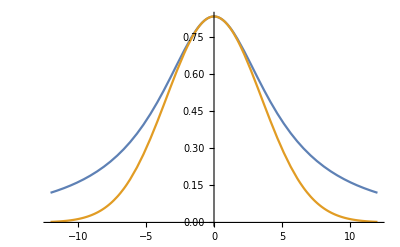

```mathematica
s = 5;
Plot[{(s/(1+s))/(1+ (4 (ν0 - ν0(1+ v/c))^2)/((1+s)Γ^2)),s/(1+s) Exp[-(4 (ν0 - ν0(1+ v/c))^2)/((1+s)Γ^2)]}, {v, -0.01vQ, 0.01 vQ}, PlotRange->All]
```

```mathematica
ClearAll[f1];
f1[s_, ν_] := f1[s, ν] = NIntegrate[
(1-s/(1 +s+ 4 (ν - ν0(1+ v/c))^2/Γ^2))
1/(1  + 4 (ν - ν0(1- v/c))^2/Γ^2)Exp[- v^2/vQ^2], {v, -2 vQ, + 2 vQ}, MaxRecursion->12];
```

## Второй вариант

```mathematica
eq = (1-s/(1 +s+ 4 (ν - ν0(1+ v/c))^2/Γ^2))1/(1  + 4 (ν - ν0(1- v/c))^2/Γ^2)Exp[- v^2/vQ^2];
eq1 =s/(1+s) 1/(1+ (2(ν - ν0(1+ v/c))/(√(1+s) Γ))^2);
eq2 = 1/(1  + (2(ν - ν0(1- v/c))/Γ)^2);
eq3 = Exp[- v^2/vQ^2];
```

```mathematica
eq1 =s/(1+s) 1/(1+ ((2 ν0 v)/(c √(1+s) Γ))^2);
eq2 = 1/(1  + ((2ν0 v)/(c Γ))^2);
eq3 = Exp[- v^2/vQ^2];
```

```mathematica
w1 = (c √(1+s) Γ)/(2 ν0);
w2 = (c Γ)/(2ν0);
w3 = vQ;
```

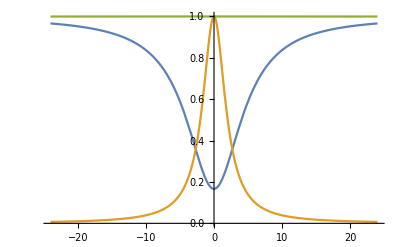

```mathematica
Plot[{1-eq1, eq2, eq3}, {v, -0.02vQ, 0.02vQ}, PlotRange->{0, Full}]
```

```mathematica
ans = Integrate[1/(1+(x/α)^2)(1-γ 1/(1+(x/β)^2)), {x, -∞, ∞}, Assumptions->{α > 0, β >0}]
```

π α (1-(β γ)/(α+β))

```mathematica
ClearAll[ν0, c, Γ, vQ, s];
```

```mathematica
FullSimplify[ans /. {α -> (c Γ)/(2ν0), β -> (c √(1+s) Γ)/(2 ν0), γ -> s/(1+s)} , s>0 && Γ >0]
```

(c π Γ)/(2 √(1+s) ν0)

```mathematica
fapp[s_] := (c π Γ)/(2 √(1+s) ν0);
```

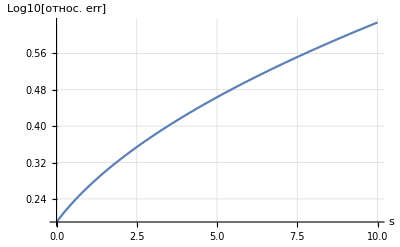

```mathematica
DiscretePlot[100 Abs[Abs[(f1[s, ν0]-fapp[s])/f1[s, ν0]]], {s, 0, 10, 0.1}, Joined->True, Filling->False, PlotRange->Full, GridLines->Automatic, AxesLabel->{"s", "Log10[относ. err]"}]
```

```mathematica
α = σ0 n l √((π m)/(8 kB T))(c  Γ)/ν0;
```

```mathematica
β = Exp[- α 1/(√(1+s))];
β0 = Exp[-α];
```

```mathematica
h = β-β0;
K = (β-β0)/(1-β0);
```

```mathematica
FullSimplify@K
```

(1-ⅇ^(α-α/(√(1+s))))/(1-ⅇ^α)

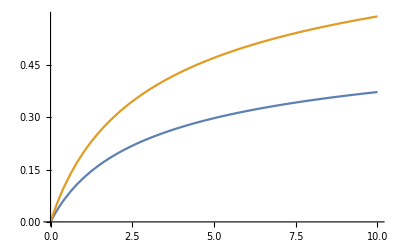

```mathematica
Plot[{h/. {α-> 1}, K /. {α-> 1}}, {s, 0, 10}]
```

## ...

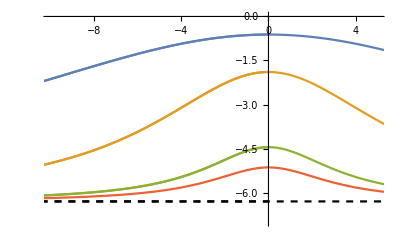

```mathematica
ϵ =4 10^-8;
image1 = Show[{
DiscretePlot[
{-f1[100, ν0+ν], -f1[10, ν0+ν], -f1[1, ν0+ν], -f1[0, ν0+ν]}, {ν,- ϵ ν0, 0, ϵ ν0 / 100}, 
PlotStyle->{, ,,{Black, Dashed}}, PlotRange->{{-10, 5}, {-7, 0}}, Filling->None
, PlotLegends->{MaTeX@"s=100",MaTeX@"s=10",MaTeX@"s=1",MaTeX@"s=0"},
Joined->True, AxesLabel->{MaTeX@"\\nu,\ \\text{MHz}", MaTeX@"\\sim \\log {I_{\\mathrm{out}}}/{I_{\\mathrm{in}}}"}]
, DiscretePlot[
{-f1[100, ν0+ν], -f1[10, ν0+ν], -f1[1, ν0+ν], -f1[1/2, ν0+ν], -f1[0, ν0+ν]}, {ν,- ϵ ν0, + ϵ ν0, ϵ ν0 / 100}, 
Filling->None, Joined->True, PlotStyle->{, ,,,{Black, Dashed}}]
}]
```

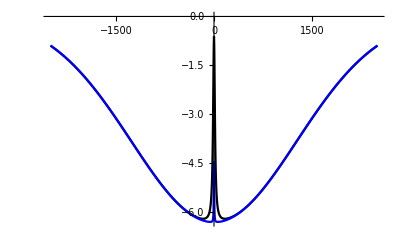

```mathematica
ϵ =8 10^-6;
image2 = DiscretePlot[
{-f1[100, ν0+ν], -f1[1, ν0+ν]}, {ν,- 0.7ϵ ν0, +0.7ϵ ν0, ϵ ν0 / 1000}, PlotRange->{Full, {Full, 0}},Filling->None, Joined->True,
PlotStyle->{Black, Blue}, PlotLegends->{MaTeX@"s=100",MaTeX@"s=10"},
AxesLabel->{MaTeX@"\\nu,\ \\text{MHz}", MaTeX@"\\sim \\log {I_{\\mathrm{out}}}/{I_{\\mathrm{in}}}"}]
```

```mathematica
(*Export[NotebookDirectory[]<>"v2.png", image2]*)
```

## Оценка контрастности

Оценим параметр κ из отношения β = I_out / I_in в глубине доплеровского провала.

```mathematica
β = 1/6; (* β = Subscript[I, out] / Subscript[I, in] *)
κx = -Log[β]/f1[0, ν0] (* c/м *)
```

0.284285

```mathematica
ClearAll[GetK];
GetK[β_, s_] :=  (β^(f1[s, ν0]/f1[0, ν0])-β)/(1-β);
```

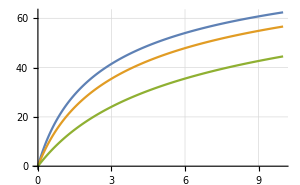

```mathematica
im3 = DiscretePlot[{100GetK[0.5, s], 100GetK[0.3, s], 100GetK[0.1, s]}, {s, 0, 10, 0.01}, Joined->True, Filling->None, (*PlotLabel->"Зависимость контрастности от параметра насыщения", *)(*PlotStyle->{RGBColor[0.,0.57,0.], Thickness[10^-2]}, *)GridLines->Automatic, AxesLabel->{MaTeX["s"], MaTeX["K,\\, \\%"]}, ImageSize->{300,150}, PlotLegends->{MaTeX["\\beta = 0.5"], MaTeX["\\beta = 0.3"], MaTeX["\\beta = 0.1"]}]
```

```mathematica
(*Export[NotebookDirectory[]<>"K.pdf", im3]*)
```

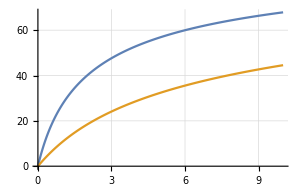

```mathematica
DiscretePlot[{100GetK[0.82, s], 100GetK[0.1, s]}, {s, 0, 10, 0.01}, Joined->True, Filling->None, (*PlotLabel->"Зависимость контрастности от параметра насыщения", *)(*PlotStyle->{RGBColor[0.,0.57,0.], Thickness[10^-2]}, *)GridLines->Automatic, AxesLabel->{MaTeX["s"], MaTeX["K,\\, \\%"]}, ImageSize->{300,150}, PlotLegends->{MaTeX["\\beta = 0.82"], MaTeX["\\beta = 0.10"]}]
```

```mathematica
β0Val = 350/428;
β0Val // N
```

0.817757

```mathematica
h1 = 400-350;
h2 = 428-350;
h1/h2 // N
```

0.641026

```mathematica
λ = 671. 10^-9;
3/(2 π)λ^2
```

2.14974×10^-13

```mathematica
λ^2
```

4.50241×10^-13

## Температурная зависимость

```mathematica
ClearAll[GetP];
GetP[T_] := 133.32 10^(10.3454 -8345.57/T-8.84 10^-5 T - 0.68106 Log10[T]);
```

```mathematica
ν0 = (3. 10^8)/(670 10^-9)/10^6; (* МГц *)
c = 3 10^8; (* м/c *)
Γ = 6 10^6 /10^6(* МГц *);
vQ = 1200;(* м/c *)
kB = 1.38 10^-23;
T = 300 + 273;
l = 0.1;
n =GetP[T]/(kB T);
Na = 6.02 10^23;
R = Na kB;
m = 0.007 / Na;
M = 0.007;
```

```mathematica
3/(2 π)λ^2  n l
```

257.532

```mathematica
(c Γ)/ν0 √((π m)/(8 kB T))
```

0.00305485

```mathematica
α[T_] := 3/(2 π)λ^2  GetP[T]/(kB T) l (c Γ)/ν0 √((π m)/(8 kB T));
α[300+273]
```

0.786722

```mathematica
β0 = Exp[-α];
β = Exp[-α/(√(1+s))];
```

```mathematica
h = β-β0
K = (β-β0)/(1-β0) // FullSimplify
```

-ⅇ^-α+ⅇ^(-α/(√(1+s)))

(1-ⅇ^(α-α/(√(1+s))))/(1-ⅇ^α)

```mathematica
hT[T_, s_:5] := -ⅇ^(-α[T])+ⅇ^(-α[T]/(√(1+s)));
```

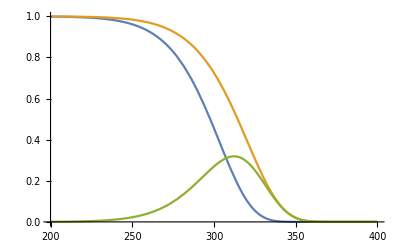

```mathematica
Plot[{ⅇ^(-α[273+T]),ⅇ^(-α[273+T]/(√(1+5))),hT[T+273]}, {T, 200, 400} ]
```

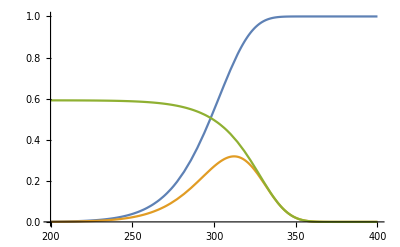

```mathematica
Plot[{1-ⅇ^(-α[273+T]),hT[T+273],hT[T+273]/(1-ⅇ^(-α[273+T])) }, {T, 200, 400}]
```